```mathematica
data1 = {{0,700},{1.1,645},{2.0,613},{2.5,591},{3.5,563},{4.3,536},{5.4,514},{6.7,488}}
```

```mathematica
{{-0.1,700},{1.1,645},{2.,613},{2.5,591},{3.5,563},{4.3,536},{5.4,514},{6.7,488}}
```

{{-0.1,700},{1.1,645},{2.,613},{2.5,591},{3.5,563},{4.3,536},{5.4,514},{6.7,488}}

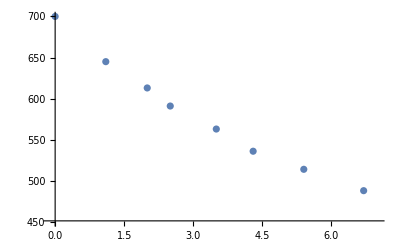

```mathematica
ListPlot[data1, PlotRange -> {{-0.1,7},{450,700}}]
```

```mathematica
freq = data1[[All,2]]
```

{700,645,613,591,563,536,514,488}

```mathematica
mass= data1[[All,1]]
```

{0,1.1,2.,2.5,3.5,4.3,5.4,6.7}

```mathematica
data2 = Table[{mass[[i]],1/(4*Pi^2*freq[[i]]^2)},{i,1, Length[mass]}]
```

{{0,1/(1960000 π^2)},{1.1,1/(1664100 π^2)},{2.,1/(1503076 π^2)},{2.5,1/(1397124 π^2)},{3.5,1/(1267876 π^2)},{4.3,1/(1149184 π^2)},{5.4,1/(1056784 π^2)},{6.7,1/(952576 π^2)}}

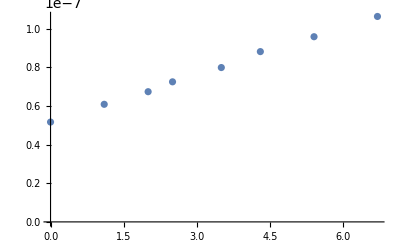

```mathematica
ListPlot[data2, PlotRange -> All]
```

```mathematica
fitline = LinearModelFit[data2, {1,x},x]
```

FittedModel[5.16925×10^-8+8.2077×10^-9 x]

```mathematica
fitline["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 5.16925×10^-8 | 4.0642×10^-10 | 127.19 | 1.59283×10^-11
x | 8.2077×10^-9 | 1.06616×10^-10 | 76.9835 | 3.23419×10^-10

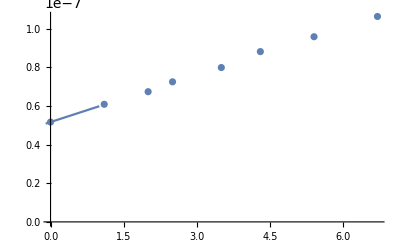

```mathematica
Show[ListPlot[data2, PlotRange -> All],Plot[fitline[x], {x, -0.1,1}]]
```

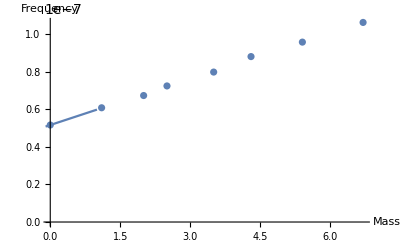

```mathematica
Show[%31,AxesLabel->{HoldForm[Mass],HoldForm[Frequency]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```